```mathematica
<<mf25.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,X],X],{X,0,n}]],X];


recipJ[n_,m_,X_]:=Collect[Normal[InverseSeries[ex[n,m,X],X]],X];
```

#### The weight of f_λ at Hecke rank m is determined in Theorem 7 of Berndt in my paper; with outer exponent j = 1/(m - 2) . By Th 7 my draft, the weight after omitting the outer exponent, as below, is 4.

```mathematica
fλNew3[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{X,0,n}],X];
Return[answer]]
```

#### The weight of f_λ is not fixed at four : weights are determined in Theorem 7 of Berndt in my paper; f_λ has weight 4 only for m = 3. From th 7, to get weight k, replace the 1/(m-2) with k/4.

```mathematica
Print[N[1/A[3]]]
```

1728.

```mathematica
Print[N[fλNew3[10,3,x]/.x->x/A[3]]];
Print[1+Sum[240*DivisorSigma[3,n]*x^n,{n,1,10}]];
Print["========================================================="];
srs=Normal[Series[fλNew3[10,3,x]^(3/2),{x,0,10}]];
Print[N[srs/.x->x/A[3]]];
Print[1-Sum[504*DivisorSigma[5,n]*x^n,{n,1,10}]];
Print["========================================================="];
srs=Normal[Series[fiNoOuterExponent[10,3,x]^(3/3),{x,0,10}]];
Print[N[srs/.x->x/A[3]]];
Print[1-Sum[504*DivisorSigma[5,n]*x^n,{n,1,10}]];
```

1.+240. x+2160. x^2+6720. x^3+17520. x^4+30240. x^5+60480. x^6+82560. x^7+140400. x^8+181680. x^9+272160. x^10

1+240 x+2160 x^2+6720 x^3+17520 x^4+30240 x^5+60480 x^6+82560 x^7+140400 x^8+181680 x^9+272160 x^10

=========================================================

1.+360. x+24840. x^2-465120. x^3+5.74175×10^7 x^4-6.80028×10^9 x^5+9.3089×10^11 x^6-1.39402×10^14 x^7+2.22503×10^16 x^8-3.72396×10^18 x^9+6.46516×10^20 x^10

1-504 x-16632 x^2-122976 x^3-532728 x^4-1575504 x^5-4058208 x^6-8471232 x^7-17047800 x^8-29883672 x^9-51991632 x^10

=========================================================

-1.+504. x+16632. x^2+122976. x^3+532728. x^4+1.5755×10^6 x^5+4.05821×10^6 x^6+8.47123×10^6 x^7+1.70478×10^7 x^8+2.98837×10^7 x^9+5.19916×10^7 x^10

1-504 x-16632 x^2-122976 x^3-532728 x^4-1575504 x^5-4058208 x^6-8471232 x^7-17047800 x^8-29883672 x^9-51991632 x^10

```mathematica
stream=OpenWrite["run24apr21no2"];
start=SessionTime[];
Clear[x];
For[m=2,m<300,m++;
expansion=fλNew3[100,m,x];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 34057.08102

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];
differences={};
m=First[First[list]];
Print[m];
f=First[list][[2]]/.x->(1728*x); (* 1728 = 1/A[3] *)
g[n_]:=240*DivisorSigma[3,n];
For[n=0,n<100,n++;
cf=Coefficient[f,x,n];
diff=cf-g[n];
AppendTo[differences,diff]];
Print[differences]
```

3

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

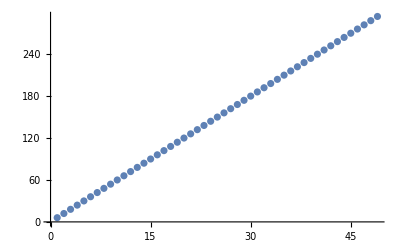

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294}}

run30apr21no21

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run30apr21no21"];

degrees={};
For[n=0,n<49,n++;
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run30apr21no21"];
list=ReadList[stream];
Close[stream];
data={};
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
numericalterm=1;
For[j=0,j<Length[fim],j++;
pair=fim[[j]];
base=pair[[1]];
power=pair[[2]];
dg=Exponent[base,x];
If[dg===0,
numericalterm=numericalterm*base^power]];
AppendTo[numerators, Numerator[numericalterm]];
AppendTo[denominators,Denominator[numericalterm]]];
Print[numerators];
Print[denominators]
```

{16,112,448,1136,2016,3136,5504,9328,12112,14112,21312,31808,35168,38528,56448,74864,78624,84784,109760,143136,154112,149184,194688,261184,252016,246176,327040,390784,390240,395136,476672,599152,596736,550368,693504,859952,810464,768320,984704,1175328,1102752,1078784,1272128,1513152,1526112,1362816,1661184,2096192,1887888}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Print[numerators/16]
```

{1,7,28,71,126,196,344,583,757,882,1332,1988,2198,2408,3528,4679,4914,5299,6860,8946,9632,9324,12168,16324,15751,15386,20440,24424,24390,24696,29792,37447,37296,34398,43344,53747,50654,48020,61544,73458,68922,67424,79508,94572,95382,85176,103824,131012,117993}

```mathematica
stream=OpenRead["run30apr21no21"];
list=ReadList[stream];
Close[stream];
Length[list]
```

49

```mathematica
stream=OpenRead["run30apr21no21"];
list=ReadList[stream];
Close[stream];
For[k=0,k<6,k++;
n=list[[k,1]];
poly=list[[k,2]];
xp=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
Print["========================================================================"];
Print["n: ",n," degree: ",xp];
Print[fim]]
```

========================================================================

n: 1 degree: 6

{16,-2+x,x^4,2+x}

========================================================================

n: 2 degree: 12

{112,-2+x,x^8,2+x,-60/7+x^2}

========================================================================

n: 3 degree: 18

{448,-2+x,x^12,2+x,7792/63-(1432 x^2)/63+x^4}

========================================================================

n: 4 degree: 24

{1136,-2+x,x^16,2+x,-5270336/1917+(1175920 x^2)/1917-(82844 x^4)/1917+x^6}

========================================================================

n: 5 degree: 30

{2016,-2+x,x^20,2+x,1218080512/14175-(892702976 x^2)/42525+(76286944 x^4)/42525-(2850704 x^6)/42525+x^8}

========================================================================

n: 6 degree: 36

{3136,-2+x,x^24,2+x,-500906023936/165375+(8431777024 x^2)/11025-(1294927232 x^4)/18375+(15044384 x^6)/4725-(4420292 x^8)/55125+x^10}

#### Above doesn’t examine the constant terms.

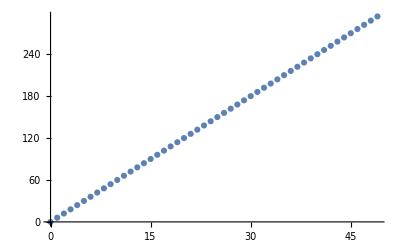

{{0,0},{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294}}

run11may21no1

```mathematica
stream=OpenRead["run24apr21no2"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run11may21no1"];

degrees={};
For[n=-1,n<49,n++;
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
monicPolynomialQ2[polynomial_,x_]:=
Module[{tf},
tf=True;
If[(PolynomialQ[polynomial,x]===False)||(leadingTermCoefficient[polynomial,x]!=1),tf==False];
Return[tf]];
```

```mathematica
specialsum3[n_]:=Module[{dv,out,table,sigma},
dv=Divisors[n];
sigma=Length[dv];
table=Table[(-1)^(n-dv[[k]])*dv[[k]]^3,{k,1,sigma}];
out=16*Total[table];
Return[out]];
```

```mathematica
stream=OpenRead["run11may21no1"];
list=ReadList[stream];
Close[stream];
yes1=0;
no1=0;
yes2=0;
no2=0;
yes3=0;
no3=0;
yes4=0;
no4=0;
yes5=0;
no5=0;


For[j=0,j<Length[list],j++;
Clear[poly];
n=list[[j,1]];
If[n>-1,
poly0=list[[j,2]];
fim=factorIntoIrreducibleMonics[poly0];
last=Last[fim][[1]];

(* question 1 *)
If[monicPolynomialQ2[last,x]===True,yes1++];
If[monicPolynomialQ2[last,x]===False,
Print["++++++++++++++++++++++++++++++++++++++++++++++++++++++"];
Print["no for n = ",n];
Print["leading term coefficient ",leadingTermCoefficient[last]];
Print["is 'last' a polynomial:  ",PolynomialQ[last,x]];
no1++];

(* question 2 *)
If[IrreduciblePolynomialQ[last]===True,yes2++];
If[IrreduciblePolynomialQ[last]===False,no2++;
Print["question 2 answer no index: ",n]];


(*question3 *)
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes3++];
If[Not[AllTrue[cl,rationalQ]],no3++];

(*question 4*)
test=Collect[specialsum3[n]*(x-2)*(x+2)*x^(4*n)*last,x];
If[poly0===test,yes4++];
If[poly0≠test,
no4++;
Print["question 4 no, index: ",n]];


(* question 5 *)
degree=Exponent[poly0,x];
If[degree===6*n,yes5++];(* conjecture 3, clause 2 *)
If[degree≠6*n,no5++];
deglast=Exponent[last,x];

] (* If[n>-1 *)
]; (* For [j *)
Print["question 1: ",{yes1,no1}];
Print["question 2: ",{yes2,no2}];Print["question 3: ",{yes3,no3}];Print["question 4: ",{yes4,no4}];Print["question 5: ",{yes5,no5}]
```

question 2 answer no index: 0

question 4 no, index: 0

question 1: {50,0}

question 2: {49,1}

question 3: {50,0}

question 4: {48,1}

question 5: {50,0}